# Doing The Elliptic Integrals

```mathematica
Clear[k,D1P,D2P,D1M,D2M,J,A,ϛP,ϡP,ϟP,RP,p2,e,b,d,c,f,B,p2,βP, αP ,ϛP,ϡP,γP,ωP ,φP,k,B,βM, αPM,ϛM,ϡM,γM,ωM,φM,Þ,ð,ϵ,RM,RP,L,a,KZ,Z2,Z1]
```

```mathematica
Clear["Global`*"]
```

## Constants

```mathematica
(r^2- 2M r + 𝒪^2)
```

```mathematica
ClearAll;
M = 1;
ℰ = 0.9`50(*COM["ℰ"];*);
ℒ =1.3`50(*COM["ℒ"];*);
𝒦= 0.5`50(*COM["𝒬"];*);
m= 0.9;
𝒪 = 0.4;
𝒩 = 0.2;
𝒮 = 0.999;
J = 1-ℰ^2;
RM = M- Sqrt[M^2- 𝒪^2];
RP = M+ Sqrt[M^2- 𝒪^2];
```

```mathematica
√(m^2 (Z2-𝒦-ℒ^2)-𝒮^2)
```

0.+1.73176 ⅈ

```mathematica
rROOTS = r/.Solve[((r 𝒩-m (r^2) ℰ)^2)/m^2-(r^2+ℒ^2+𝒦) (r^2- 2M r + 𝒪^2)==0==0,r]
zROOTS = z/.Solve[-z^2 (𝒦+ℒ^2+𝒮^2/m^2)-(2 z ℒ 𝒮)/m+ 𝒦==0,z]
```

{0.0834474,0.580596-1.65604 ⅈ,0.580596+1.65604 ⅈ,7.17641}

{-0.990807,0.147465}

### Solving the Radial Solution

```mathematica
RPoly[r_]:=((r 𝒩-m (r^2) ℰ)^2)/m^2-(r^2+ℒ^2+𝒦) (r^2- 2M r + 𝒪^2);



r4=((𝒦 +ℒ^2) 𝒪^2)/(rI^3 (1-ℰ^2))
```

```mathematica
Collect[(1-ℰ^2)(rI-r)^3(r-r4)-(((r 𝒩-m (r^2) ℰ)^2)/m^2-(r^2+ℒ^2+𝒦) (r^2- 2M r + 𝒪^2)), r]
```

```mathematica
Solve[-r4 rI^3 (1-ℰ^2)+𝒦 𝒪^2+ℒ^2 𝒪^2==0, r4]
```

```mathematica
r4=((𝒦 +ℒ^2) 𝒪^2)/(rI^3 (1-ℰ^2))
```

### Solving the Polar Equation

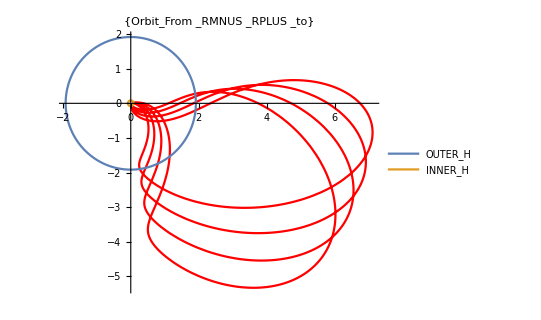

```mathematica
Z1 =- (m (ℒ 𝒮+√((𝒦+ℒ^2) (m^2 𝒦+𝒮^2))))/(m^2 (𝒦+ℒ^2)+𝒮^2);
Z2 =(𝒦+ℒ^2+𝒮^2/m^2) (m (-ℒ 𝒮+√((𝒦+ℒ^2) (m^2 𝒦+𝒮^2))))/(m^2 (𝒦+ℒ^2)+𝒮^2);
MINOZ[z_]:=-(2 m  ArcTan[(m √(Z2-z (𝒦+ℒ^2)-(z 𝒮^2)/m^2))/(√(z-Z1) √(m^2 (𝒦+ℒ^2)+𝒮^2))])/(√(m^2 (𝒦+ℒ^2)+𝒮^2))
z[λ_]:= (m^2 Z2 Cos[(√(m^2 (𝒦+ℒ^2)+𝒮^2) λ)/(2 m)]^2)/(m^2 (𝒦+ℒ^2)+𝒮^2)+Z1 Sin[(√(m^2 (𝒦+ℒ^2)+𝒮^2) λ)/(2 m)]^2
θ[λ_]:= ArcCos[z[λ]]
Q1 = ParametricPlot[{r[λ]*Sin[θ[λ]],r[λ]Cos[θ[λ]]}, {λ,0,20}, PlotRange->All, PlotLabel->{Orbit_From_RPLUS_to_RMNUS}, PlotStyle->Red, PlotLegends->ORBIT];
Q2 = ParametricPlot[{{RP*Cos[u],RP Sin[u]},{RM*Cos[u],RM Sin[u]}},{u,-π,π},MaxRecursion->12,PlotRange->All,PlotLegends->{OUTER_H,INNER_H}];
Show[Q1,Q2]
```

### Solving the Aimuthal Equation

```mathematica
Integrate[(𝒮 z+m (ℒ))/(m(1-z^2)) 1/Sqrt[(z-Z1)(Z2-(𝒦+ℒ^2+𝒮^2/m^2)z)], z]
```

```mathematica
MINOZ[z_]:=( (m ℒ+𝒮) ArcTan[(m √(-1+Z1) √(Z2-z (𝒦+ℒ^2)-(z 𝒮^2)/m^2))/(√(z-Z1) √(m^2 (Z2-𝒦-ℒ^2)-𝒮^2))])/(√(-1+Z1)  √(m^2 (Z2-𝒦-ℒ^2)-𝒮^2))+((-m ℒ+𝒮)  ArcTan[(m √(1+Z1) √(Z2-z (𝒦+ℒ^2)-(z 𝒮^2)/m^2))/(√(z-Z1) √(m^2 (Z2+𝒦+ℒ^2)+𝒮^2))])/(√(1+Z1)  √(m^2 (Z2+𝒦+ℒ^2)+𝒮^2))
ϕ[λ_]:=((m ℒ-𝒮) ArcTan[(√(1+Z1)√(m^2 (𝒦+ℒ^2)+𝒮^2)Tan[(√(m^2 (𝒦+ℒ^2)+𝒮^2) λ)/(2 m)])/(√(m^2 (Z2+𝒦+ℒ^2)+𝒮^2))])/(√(1+Z1) √(m^2 (Z2+𝒦+ℒ^2)+𝒮^2))-((m ℒ+𝒮) ArcTan[(√(-1+Z1) √(m^2 (𝒦+ℒ^2)+𝒮^2) Tan[(√(m^2 (𝒦+ℒ^2)+𝒮^2) λ)/(2 m)])/(√(m^2 (Z2-𝒦-ℒ^2)-𝒮^2))])/(√(-1+Z1) √(m^2 (Z2-𝒦-ℒ^2)-𝒮^2))
```

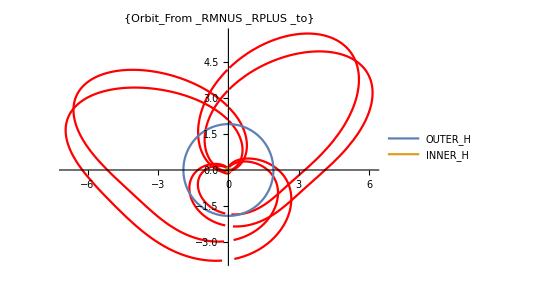

```mathematica
Q1 = ParametricPlot[{Re[r[λ]]*Sin[Re[ϕ[λ]]],Re[r[λ]]Cos[Re[ϕ[λ]]]}, {λ,0,20}, PlotRange->All, PlotLabel->{Orbit_From_RPLUS_to_RMNUS}, PlotStyle->Red, PlotLegends->ORBIT];
Q2 = ParametricPlot[{{RP*Cos[u],RP Sin[u]},{RM*Cos[u],RM Sin[u]}},{u,-π,π},MaxRecursion->12,PlotRange->All,PlotLegends->{OUTER_H,INNER_H}];
Show[Q1,Q2]
```

```mathematica
P1 = ParametricPlot3D[{Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]},{λ,50,100}, PlotStyle->Red,PlotRange->All];
P2 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},MaxRecursion->9,PlotStyle->{Opacity[1],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];
Show[P1,P2]
```

#### Time Solutions

```mathematica
Expand[((r^2) (-𝒩 r+m (r^2) ℰ))/(m (r-rP)(r-rM))]
```

(r^4 ℰ)/((r-rM) (r-rP))-(r^3 𝒩)/(m (r-rM) (r-rP))

### Analysis

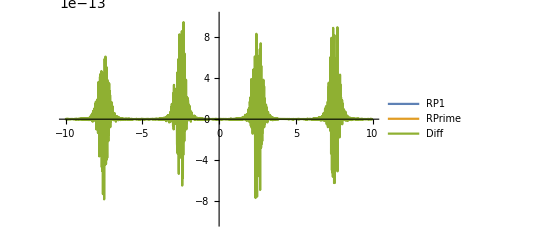

```mathematica
RPoly1[r_]:= ((r 𝒩-m (r^2) ℰ)^2)/m^2-(r^2+ℒ^2+𝒦) (r^2- 2M r + 𝒪^2)

Plot[{RPoly1[r[λ]], (r'[λ])^2, (r'[λ])^2- RPoly1[r[λ]]},{λ,-10,10}, PlotLegends->{RP1,RPrime,Diff},  PlotRange->{{-10,10},{-0.0000000000010,0.0000000000010}}]
```

```mathematica
Polyθ[2]
```

3.11016-3.4221 z^2

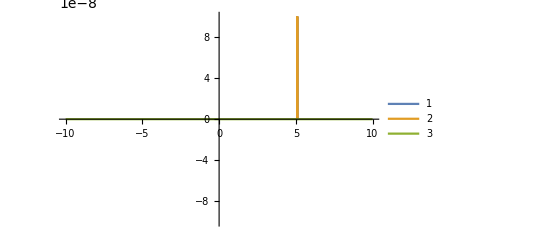

```mathematica
Polyθ[λ_] :=-z[λ]^2 (𝒦+ℒ^2+𝒮^2/m^2)-(2 z[λ] ℒ 𝒮)/m+ 𝒦
Plot[{(z'[λ])^2, Polyθ[λ], (z'[λ])^2- Polyθ[λ]}, {λ,-10,10}, PlotLegends->Automatic ,PlotLegends->{PolyθQ,θQ,θQ-PolyθQ}, PlotRange->{{-10,10}, {-0.0000001,0.0000001}}]
```

```mathematica
|
```

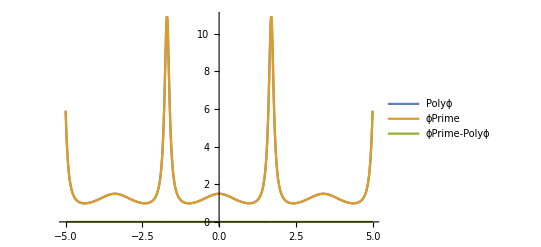

```mathematica
(*Plot[Im[ϕ[λ]],{λ,-5,5}]*)
Polyϕ[λ_]:= (𝒮 z[λ]+m (ℒ))/(m(1-z[λ]^2)) 
Plot[{Polyϕ[λ],Re[ϕ'[λ]],Re[ϕ'[λ]-Polyϕ[λ]]},{λ,-5,5}, PlotRange->All,PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ}]
```